```mathematica
(* Seeing if can determine B^x along x-dir to one higher order than lowest order *)
(* Sasha would determine dBdx's polynomial coefficients for left and right cells centered on cell center, where point-valued dBx/dx is known from differencing a2c_i B^i across cell center *)
(* Here x/dx=0 is cell center, x/dx=1/2 is right cell face of interest and x/dx=-1/2 is the left cell face of interest *)
dBdxraw:=F0+F1/dx (x/dx-0) + F2 /dx(x/dx-0)^2+ F3 /dx(x/dx-0)^3+ F4 /dx(x/dx-0)^4;
```

```mathematica
(* The dBdxraw has constraints, but let place them later through the use of the a2c_i function *)
```

```mathematica
(* Now form integral that is distribution of Bx in the left and right cell with Bxl0 and Bxr0 cell center point values of field *)
Bx:=Bx0+Integrate[Evaluate[dBdxraw],{x,0*dx,t}]
```

```mathematica
(* Now setup equation that determines Bxl0, that is a2c_i B^i = known quantity *)
(* We want to form a2c_i B^i, which requires forming another function f=a2c_i Bx such that c2a_i f=Bx *)
f:=f0+f1/dx (x/dx-0) + f2 /dx(x/dx-0)^2+ f3 /dx(x/dx-0)^3+ f4 /dx(x/dx-0)^4+ f5 /dx(x/dx-0)^5;
RunningAverage:=Integrate[f,{t,x-dx/2,x+dx/2}]/dx;
```

```mathematica
(* Now obtain coefficients of f from those of Bx *)
```

```mathematica
sol=Solve[CoefficientList[RunningAverage,x] ==CoefficientList[Bx,t],{f0,f1,f2,f3,f4,f5}]
```

{{f0→Bx0,f1→dx^2 F0,f2→(dx F1)/2,f3→(dx F2)/3,f4→(dx F3)/4,f5→(dx F4)/5}}

```mathematica
a2cBx=f//.sol[[1]]
```

Bx0+F0 x+(F1 x^2)/(2 dx^2)+(F2 x^3)/(3 dx^3)+(F3 x^4)/(4 dx^4)+(F4 x^5)/(5 dx^5)

```mathematica
(* now have a2c_i B^i distribution that has to give back known a2c_i B^i's, use this to obtain Bxl0 and Bxr0 assuming rest will correctly give back correct distribution of B^i *)
```

```mathematica
fun1=FullSimplify[a2cBx//.{x->1/2*dx}]
fun2=FullSimplify[a2cBx//.{x->-1/2*dx}]
sol=FullSimplify[Solve[{fun1==a2cright,fun2==a2cleft},{Bx0,F0}]]
FullSimplify[(fun1-fun2)/dx//.sol[[1]]]
```

Bx0+1/960 (5 (96 dx F0+24 F1+8 F2+3 F3)+6 F4)

Bx0+1/960 (-480 dx F0+120 F1-40 F2+15 F3-6 F4)

{{Bx0→1/64 (32 a2cleft+32 a2cright-8 F1-F3),F0→-(20 (12 a2cleft-12 a2cright+F2)+3 F4)/(240 dx)}}

(-a2cleft+a2cright)/dx

```mathematica
(* Get final Bxl and Bxr distributions *)
```

```mathematica
myBx=FullSimplify[Bx//.sol[[1]]]
```

(480 a2cleft dx^4 (dx-2 t)+480 a2cright dx^4 (dx+2 t)-(dx^2-4 t^2) (15 dx^3 (8 F1+F3)+4 dx^2 (20 F2+3 F4) t+60 dx F3 t^2+48 F4 t^3))/(960 dx^5)

0.65+0.3 t

0.12 (1.55782+t) (3.75741+(-1.24826+t) t) (0.654002+t (0.1071+t))

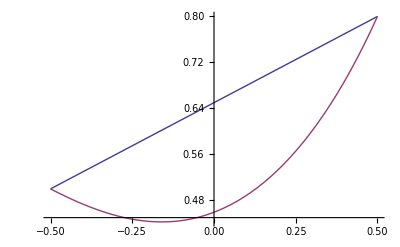

```mathematica
toplotBxlinear=FullSimplify[myBx//.{dx->1,a2cleft->.5,a2cright->.8,F1->0,F2->0,F3->0,F4->0}]
toplotBxnonlinear=FullSimplify[myBx//.{dx->1,a2cleft->.5,a2cright->.8,F1->1.5,F2->.9,F3->.2,F4->.6}]
Plot[{toplotBxlinear,toplotBxnonlinear},{t,-1/2,1/2}]
```

```mathematica
(* Get final a2c_i B^i distributions *)
mya2cBx=FullSimplify[a2cBx//.sol[[1]]]
```

(160 a2cleft dx^2 (dx^3-8 x^3)+160 a2cright dx^2 (dx^3+8 x^3)-(dx^2-4 x^2) (20 dx F3 x^2+16 F4 x^3+5 dx^3 (8 F1+F3-64 F0 x)))/(320 dx^5)

```mathematica
(* Check how a2cB^i is set *)
```

```mathematica
FullSimplify[mya2cBx//.{x->1/2*dx}]
FullSimplify[mya2cBx//.{x->-1/2*dx}]
```

a2cright

a2cleft

```mathematica
(* We DO get back a2cB at the face! good. *)
```

```mathematica
(* Assume don't care if face point values are different *)
```

```mathematica
(* Get point values at faces just to see *)
```

```mathematica
FullSimplify[myBx//.{t->1/2*dx}]
FullSimplify[myBx//.{t->-1/2*dx}]
```

a2cright

a2cleft

```mathematica
(* no change? *)
```